## Set your path to NonLinearSolver and get it

```mathematica
dddRicardo="/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m";
```

```mathematica
1
```

1

### DataToEquations and the critical congestion solver

```mathematica
Get[dddRicardo]
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1}, {7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9}, {7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e = Data2Equations[Data/.{I1->52,I2->104,U1->0,U2->0, U3->0}];
crit=CriticalCongestionSolver[d2e];//AbsoluteTiming
```

1: {True,jt10≥0&&jt11≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥208+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&780+11 jt10+jt32+jt33+jt34≥11 jt17+11 jt18+jt29&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45≥22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33&&364+8 jt10+jt19+jt29+jt30+u1≤9 jt17+9 jt18+jt22+jt34+jt37&&43 jt17+43 jt18+jt19+jt29+jt30+u1≤3328+44 jt10+jt22+jt34+jt37&&3276+52 jt10+3 jt22+3 jt34+3 jt37+u1≤49 jt17+49 jt18+3 (jt19+jt29+jt30)&&jt11≤104&&jt19+jt32≤jt10+jt22&&4 jt17+4 jt18+jt41+jt42≤364+4 jt10+jt27+jt28&&jt11+jt16≤jt17+jt18&&jt17+jt18≤52+jt11+jt16&&jt27≤jt16&&jt16≤jt17+jt22+jt27&&208+3 jt10+jt19≤4 jt17+3 jt18+jt22&&208+3 jt10+jt28≤4 jt17+3 jt18+jt22&&5 jt17+4 jt18+jt22≤364+4 jt10+jt16+jt28&&jt17+jt18≤156+jt10+jt16&&11 jt17+11 jt18+jt44+jt45≤780+11 jt10+jt32+jt33+jt34&&jt44+jt47≤jt27+jt28&&jt41+jt48≤jt32+jt33+jt34&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&35 jt10+2 (1170+jt22+jt34+jt37)≤33 jt17+33 jt18+2 (jt19+jt29+jt30)&&780+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37≤11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48&&1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48≤22 jt17+22 jt18+jt19+jt27+jt28+jt29+2 jt30+jt32+2 jt33,(jt11+jt16==0||52+jt10+jt11+jt16==jt17+jt18)&&(jt10==0||jt17+jt18==0)&&(jt16==0||156+jt10+jt16==jt17+jt18)&&(208+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(jt10+jt22==jt19||208+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(jt27+jt28==0||4 (jt17+jt18)==364+4 jt10+jt27+jt28)&&(jt32+jt33+jt34==0||11 (jt17+jt18)==780+11 jt10+jt32+jt33+jt34)&&(780+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(jt10==0||jt11+jt16==0)&&(52+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt17==0||jt19==0)&&(jt18==0||jt10==jt19)&&(208+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(208+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(364+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt29==0||jt32==0)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt33==0||780+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(364+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt45==0||jt48==0)&&(780+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||780+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(208+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||364+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(2704+38 jt10+jt22+jt34+jt37==37 jt17+37 jt18+jt19+jt29+jt30||3328+44 jt10+jt22+jt34+jt37==43 jt17+43 jt18+jt19+jt29+jt30+u1)&&(35 jt10+2 (1170+jt22+jt34+jt37)==33 jt17+33 jt18+2 (jt19+jt29+jt30)||3276+52 jt10+3 jt22+3 jt34+3 jt37+u1==49 jt17+49 jt18+3 (jt19+jt29+jt30))}

Iterative DNF convertion took 5.96039 seconds to terminate.

Reducing took 0.014069 seconds to terminate.

1: {True,True,(0≤jt34<1&&jt30==18+jt34&&jt30+jt33==19&&jt37==0)||(jt34==1&&jt30==19&&jt33==0&&jt37==0)}

Iterative DNF convertion took 0.006609 seconds to terminate.

Reducing took 0.004034 seconds to terminate.

1: {True,18≤jt30≤19,True}

1: {True,18≤jt30≤19,True}

1: {True,18≤jt30≤19,True}

MFGSS: Multiple solutions: 18.≤jt30≤19.

Picked one value for the variable(s) {jt30} {18.} (respectively)

{7.05552,Null}

Iterative DNF convertion...

... took 5.84058 seconds to terminate. 
Removing duplicates and reducing...

... took 0.010532 seconds to terminate.

Iterative DNF convertion...

... took 0.00417 seconds to terminate. 
Removing duplicates and reducing...

... took 0.002711 seconds to terminate.

Iterative DNF convertion...

... took 6.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

... took 0.000177 seconds to terminate.

Iterative DNF convertion...

... took 5.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

... took 0.000151 seconds to terminate.

Iterative DNF convertion...

... took 4.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

... took 0.000142 seconds to terminate.

MFGSS: Multiple solutions: 18.≤jt30≤19.

Picked one value for the variable(s) {jt30} {18.} (respectively)

{6.78183,Null}

Iterative DNF convertion took 5.97392 seconds to terminate

Iterative DNF convertion took 0.109029 seconds to terminate

Iterative DNF convertion took 0.011164 seconds to terminate

Iterative DNF convertion took 0.008277 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18.≤jt30≤19.

Picked one value for the variable(s) {jt30} {18.} (respectively)

{7.00537,Null}

Iterative DNF convertion took 6.05701 seconds to terminate

Iterative DNF convertion took 0.100968 seconds to terminate

Iterative DNF convertion took 0.010943 seconds to terminate

Iterative DNF convertion took 0.00805 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18.≤jt30≤19.

Picked one value for the variable(s) {jt30} {18.} (respectively)

{7.07742,Null}

Iterative DNF convertion took 5.50677 seconds to terminate

Iterative DNF convertion took 0.103426 seconds to terminate

Iterative DNF convertion took 0.010735 seconds to terminate

Iterative DNF convertion took 0.00777 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18.≤jt30≤19.

Picked one value for the variable(s) {jt30} {18.} (respectively)

{6.51655,Null}

Iterative DNF convertion took 6.0341 seconds to terminate

Iterative DNF convertion took 0.101598 seconds to terminate

Iterative DNF convertion took 0.010431 seconds to terminate

Iterative DNF convertion took 0.007378 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18.≤jt30≤19.

Picked one value for the variable(s) {jt30} {18.} (respectively)

{7.03821,Null}

Iterative DNF convertion took 8.55197 seconds to terminate

Iterative DNF convertion took 0.120352 seconds to terminate

Iterative DNF convertion took 0.013192 seconds to terminate

Iterative DNF convertion took 0.009059 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18.≤jt30≤19.

Picked one value for the variable(s) {jt30} {18.} (respectively)

{9.5936,Null}

Iterative DNF convertion took 7.67921 seconds to terminate

Iterative DNF convertion took 0.18949 seconds to terminate

Iterative DNF convertion took 0.026459 seconds to terminate

Iterative DNF convertion took 0.008881 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18.≤jt30≤19.

Picked one value for the variable(s) {jt30} {18.} (respectively)

{8.80256,Null}

```mathematica
IsNonLinearSolution[crit]@crit["AssoCritical"]
```

All restrictions are True

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {-5.68434×10^-14,-1.13687×10^-13,2.13163×10^-14,-8.52651×10^-14,-9.9476×10^-14,5.32907×10^-15,-8.52651×10^-14,-8.52651×10^-14,1.11022×10^-15,-2.13163×10^-14,-6.39488×10^-14,-2.13163×10^-14,-6.39488×10^-14,-4.26326×10^-14}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 1.13687×10^-13

<|u1→257.,u2→205.,u3→328.,u4→224.,u5→205.,u6→224.,u7→205.,u8→134.,u9→224.,u10→139.,u11→134.,u12→139.,u13→134.,u14→58.,u15→139.,u16→59.,u17→58.,u18→59.,u19→58.,u20→39.,u21→58.,u22→0.,u23→59.,u24→39.,u25→59.,u26→0.,u27→39.,u28→0.,u29→0.,u30→0.,u31→0.,u32→0.,u33→0.,u34→0.,u35→257.,u36→257.,u37→328.,u38→328.,j1→0.,j2→52.,j3→0.,j4→104.,j5→19.,j6→0.,j7→0.,j8→71.,j9→0.,j10→85.,j11→5.,j12→0.,j13→0.,j14→76.,j15→0.,j16→80.,j17→1.,j18→0.,j19→0.,j20→19.,j21→0.,j22→58.,j23→0.,j24→20.,j25→0.,j26→59.,j27→0.,j28→39.,j29→0.,j30→58.,j31→0.,j32→59.,j33→0.,j34→39.,j35→0.,j36→52.,j37→0.,j38→104.,jt1→0.,jt2→52.,jt3→0.,jt4→104.,jt5→0.,jt6→52.,jt7→0.,jt8→19.,jt9→0.,jt10→0.,jt11→19.,jt12→85.,jt13→0.,jt14→0.,jt15→0.,jt16→0.,jt17→0.,jt18→71.,jt19→0.,jt20→5.,jt21→0.,jt22→0.,jt23→5.,jt24→80.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→18.,jt31→58.,jt32→0.,jt33→1.,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt39→0.,jt40→0.,jt41→1.,jt42→20.,jt43→59.,jt44→0.,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt50→0.,jt51→0.,jt52→0.,jt53→0.,jt54→19.,jt55→0.,jt56→20.,jt57→0.,jt58→0.,jt59→58.,jt60→0.,jt61→59.,jt62→0.,jt63→39.,jt64→0.|>

#### Non-critical congestion solver

#### Starting from the critical congestion solution

```mathematica
Get[dddRicardo]
alpha[edge_]:=0.2
nn=NonLinear[crit];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]];
```

Iterative DNF convertion took 11.1371 seconds to terminate

Iterative DNF convertion took 0.117163 seconds to terminate

Iterative DNF convertion took 0.010788 seconds to terminate

Iterative DNF convertion took 0.006877 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 17.0303≤jt30≤17.8078

Picked one value for the variable(s) {jt30} {17.0303} (respectively)

{45.4072,95.1078,-14.7424,63.4576,76.8485,-2.64056,68.2328,72.0589,0.108731,14.7424,51.0885,15.646,52.0373,33.1792}
{45.4072,95.1078,-14.3189,63.0095,77.2988,-2.54621,67.6691,72.6235,0.199014,13.669,51.4489,15.2819,53.1905,31.6888}

Max error for non-linear solution: 1.49036

Iterative DNF convertion took 11.3288 seconds to terminate

Iterative DNF convertion took 0.108405 seconds to terminate

Iterative DNF convertion took 0.015231 seconds to terminate

Iterative DNF convertion took 0.008441 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 16.0909≤jt30≤16.7337

Picked one value for the variable(s) {jt30} {16.0909} (respectively)

{45.4072,95.1078,-14.3189,63.0095,77.2988,-2.54621,67.6691,72.6235,0.199014,13.669,51.4489,15.2819,53.1905,31.6888}
{45.4072,95.1078,-13.914,62.5803,77.7303,-2.45043,67.1223,73.1714,0.24207,12.706,51.7973,14.9125,54.2503,30.3053}

Max error for non-linear solution: 1.38356

Iterative DNF convertion took 10.9651 seconds to terminate

Iterative DNF convertion took 0.114088 seconds to terminate

Iterative DNF convertion took 0.011885 seconds to terminate

Iterative DNF convertion took 0.009355 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 15.1932≤jt30≤15.7633

Picked one value for the variable(s) {jt30} {15.1932} (respectively)

{45.4072,95.1078,-13.914,62.5803,77.7303,-2.45043,67.1223,73.1714,0.24207,12.706,51.7973,14.9125,54.2503,30.3053}
{45.4072,95.1078,-13.5276,62.1702,78.1426,-2.35677,66.5967,73.6981,0.260444,11.8395,52.1272,14.5458,55.2285,29.0228}

Max error for non-linear solution: 1.2825

Iterative DNF convertion took 11.4849 seconds to terminate

Iterative DNF convertion took 0.116271 seconds to terminate

Iterative DNF convertion took 0.017307 seconds to terminate

Iterative DNF convertion took 0.007194 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 14.3473≤jt30≤14.8831

Picked one value for the variable(s) {jt30} {14.3473} (respectively)

{45.4072,95.1078,-13.5276,62.1702,78.1426,-2.35677,66.5967,73.6981,0.260444,11.8395,52.1272,14.5458,55.2285,29.0228}
{45.4072,95.1078,-13.16,61.7795,78.5355,-2.26814,66.0963,74.1999,0.267648,11.0568,52.4328,14.1887,56.1361,27.8357}

Max error for non-linear solution: 1.18708

Iterative DNF convertion took 11.052 seconds to terminate

Iterative DNF convertion took 0.134473 seconds to terminate

Iterative DNF convertion took 0.018144 seconds to terminate

Iterative DNF convertion took 0.009215 seconds to terminate

Iterative DNF convertion took 0.000014 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 13.5593≤jt30≤14.0822

Picked one value for the variable(s) {jt30} {13.5593} (respectively)

{45.4072,95.1078,-13.16,61.7795,78.5355,-2.26814,66.0963,74.1999,0.267648,11.0568,52.4328,14.1887,56.1361,27.8357}
{45.4072,95.1078,-12.8111,61.4082,78.9091,-2.18632,65.6233,74.6743,0.270076,10.3476,52.7107,13.846,56.9817,26.7385}

Max error for non-linear solution: 1.09717

Iterative DNF convertion took 11.5447 seconds to terminate

Iterative DNF convertion took 0.111107 seconds to terminate

Iterative DNF convertion took 0.013031 seconds to terminate

Iterative DNF convertion took 0.007195 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 12.8312≤jt30≤13.3524

Picked one value for the variable(s) {jt30} {12.8312} (respectively)

{45.4072,95.1078,-12.8111,61.4082,78.9091,-2.18632,65.6233,74.6743,0.270076,10.3476,52.7107,13.846,56.9817,26.7385}
{45.4072,95.1078,-12.4805,61.0559,79.2636,-2.11196,65.1783,75.1208,0.270397,9.70397,52.9595,13.5202,57.772,25.7259}

Max error for non-linear solution: 1.01262

Iterative DNF convertion took 11.73 seconds to terminate

Iterative DNF convertion took 0.100672 seconds to terminate

Iterative DNF convertion took 0.013234 seconds to terminate

Iterative DNF convertion took 0.00832 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 12.1624≤jt30≤12.6873

Picked one value for the variable(s) {jt30} {12.1624} (respectively)

{45.4072,95.1078,-12.4805,61.0559,79.2636,-2.11196,65.1783,75.1208,0.270397,9.70397,52.9595,13.5202,57.772,25.7259}
{45.4072,95.1078,-12.1679,60.7223,79.5994,-2.04499,64.7608,75.5398,0.269723,9.11982,53.1793,13.2122,58.5116,24.7926}

Max error for non-linear solution: 0.933278

Iterative DNF convertion took 11.5287 seconds to terminate

Iterative DNF convertion took 0.125275 seconds to terminate

Iterative DNF convertion took 0.015408 seconds to terminate

Iterative DNF convertion took 0.008788 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 11.5506≤jt30≤12.0817

Picked one value for the variable(s) {jt30} {11.5506} (respectively)

{45.4072,95.1078,-12.1679,60.7223,79.5994,-2.04499,64.7608,75.5398,0.269723,9.11982,53.1793,13.2122,58.5116,24.7926}
{45.4072,95.1078,-11.8725,60.4066,79.9172,-1.98495,64.3697,75.9325,0.268554,8.5901,53.3712,12.9218,59.2043,23.9337}

Max error for non-linear solution: 0.858975

Iterative DNF convertion took 12.5966 seconds to terminate

Iterative DNF convertion took 0.118152 seconds to terminate

Iterative DNF convertion took 0.012684 seconds to terminate

Iterative DNF convertion took 0.007912 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 10.9927≤jt30≤11.5311

Picked one value for the variable(s) {jt30} {10.9927} (respectively)

{45.4072,95.1078,-11.8725,60.4066,79.9172,-1.98495,64.3697,75.9325,0.268554,8.5901,53.3712,12.9218,59.2043,23.9337}
{45.4072,95.1078,-11.5937,60.1083,80.2176,-1.93122,64.0036,76.3001,0.267133,8.11041,53.5368,12.6488,59.8533,23.1441}

Max error for non-linear solution: 0.789537

Iterative DNF convertion took 11.3249 seconds to terminate

Iterative DNF convertion took 0.12799 seconds to terminate

Iterative DNF convertion took 0.013357 seconds to terminate

Iterative DNF convertion took 0.007052 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 10.4852≤jt30≤11.0313

Picked one value for the variable(s) {jt30} {10.4852} (respectively)

{45.4072,95.1078,-11.5937,60.1083,80.2176,-1.93122,64.0036,76.3001,0.267133,8.11041,53.5368,12.6488,59.8533,23.1441}
{45.4072,95.1078,-11.3307,59.8266,80.5014,-1.88314,63.661,76.6442,0.265589,7.67675,53.6778,12.3924,60.4613,22.4193}

Max error for non-linear solution: 0.724781

Iterative DNF convertion took 10.9748 seconds to terminate

Iterative DNF convertion took 0.109243 seconds to terminate

Iterative DNF convertion took 0.015662 seconds to terminate

Iterative DNF convertion took 0.009266 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 10.0248≤jt30≤10.5786

Picked one value for the variable(s) {jt30} {10.0248} (respectively)

{45.4072,95.1078,-11.3307,59.8266,80.5014,-1.88314,63.661,76.6442,0.265589,7.67675,53.6778,12.3924,60.4613,22.4193}
{45.4072,95.1078,-11.0829,59.5608,80.7692,-1.84008,63.3405,76.9662,0.264,7.28538,53.7961,12.1519,61.0308,21.7548}

Max error for non-linear solution: 0.664517

Iterative DNF convertion took 12.5463 seconds to terminate

Iterative DNF convertion took 0.11691 seconds to terminate

Iterative DNF convertion took 0.014518 seconds to terminate

Iterative DNF convertion took 0.007207 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 9.60795≤jt30≤10.1692

Picked one value for the variable(s) {jt30} {9.60795} (respectively)

{45.4072,95.1078,-11.0829,59.5608,80.7692,-1.84008,63.3405,76.9662,0.264,7.28538,53.7961,12.1519,61.0308,21.7548}
{45.4072,95.1078,-10.8495,59.3101,81.0218,-1.80144,63.0407,77.2675,0.262411,6.93279,53.8935,11.9264,61.5644,21.1463}

Max error for non-linear solution: 0.608551

Iterative DNF convertion took 11.1132 seconds to terminate

Iterative DNF convertion took 0.124612 seconds to terminate

Iterative DNF convertion took 0.016628 seconds to terminate

Iterative DNF convertion took 0.009451 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 9.23134≤jt30≤9.79959

Picked one value for the variable(s) {jt30} {9.23134} (respectively)

{45.4072,95.1078,-10.8495,59.3101,81.0218,-1.80144,63.0407,77.2675,0.262411,6.93279,53.8935,11.9264,61.5644,21.1463}
{45.4072,95.1078,-10.6298,59.0739,81.2599,-1.76668,62.7601,77.5495,0.260859,6.61568,53.9719,11.7153,62.064,20.5896}

Max error for non-linear solution: 0.556681

Iterative DNF convertion took 11.375 seconds to terminate

Iterative DNF convertion took 0.116888 seconds to terminate

Iterative DNF convertion took 0.014767 seconds to terminate

Iterative DNF convertion took 0.007642 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 8.89177≤jt30≤9.46662

Picked one value for the variable(s) {jt30} {8.89177} (respectively)

{45.4072,95.1078,-10.6298,59.0739,81.2599,-1.76668,62.7601,77.5495,0.260859,6.61568,53.9719,11.7153,62.064,20.5896}
{45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}

Max error for non-linear solution: 0.508702

Iterative DNF convertion took 11.0086 seconds to terminate

Iterative DNF convertion took 0.109171 seconds to terminate

Iterative DNF convertion took 0.015896 seconds to terminate

Iterative DNF convertion took 0.007361 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 8.58617≤jt30≤9.16714

Picked one value for the variable(s) {jt30} {8.58617} (respectively)

{45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}
{45.4072,95.1078,-10.2287,58.6419,81.6953,-1.70694,62.2517,78.0607,0.257955,6.07572,54.0784,11.3331,62.9701,19.6165}

Max error for non-linear solution: 0.464406

Iterated 15 times out of 15

{187.336,Null}

All restrictions are True

Nlhs: {45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {45.4072,95.1078,-10.2287,58.6419,81.6953,-1.70694,62.2517,78.0607,0.257955,6.07572,54.0784,11.3331,62.9701,19.6165}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 0.464406

Iterative DNF convertion took 13.6054 seconds to terminate

Iterative DNF convertion took 0.064656 seconds to terminate

Iterative DNF convertion took 0.008541 seconds to terminate

Iterative DNF convertion took 0.007706 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 17.0303≤jt30≤17.8078

Picked one value for the variable(s) {jt30} {17.0303} (respectively)

{45.4072,95.1078,-14.7424,63.4576,76.8485,-2.64056,68.2328,72.0589,0.108731,14.7424,51.0885,15.646,52.0373,33.1792}
{45.4072,95.1078,-14.3189,63.0095,77.2988,-2.54621,67.6691,72.6235,0.199014,13.669,51.4489,15.2819,53.1905,31.6888}

Max error for non-linear solution: 1.49036

Iterative DNF convertion took 13.7571 seconds to terminate

Iterative DNF convertion took 0.075117 seconds to terminate

Iterative DNF convertion took 0.009118 seconds to terminate

Iterative DNF convertion took 0.009003 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 16.0909≤jt30≤16.7337

Picked one value for the variable(s) {jt30} {16.0909} (respectively)

{45.4072,95.1078,-14.3189,63.0095,77.2988,-2.54621,67.6691,72.6235,0.199014,13.669,51.4489,15.2819,53.1905,31.6888}
{45.4072,95.1078,-13.914,62.5803,77.7303,-2.45043,67.1223,73.1714,0.24207,12.706,51.7973,14.9125,54.2503,30.3053}

Max error for non-linear solution: 1.38356

Iterative DNF convertion took 13.2052 seconds to terminate

Iterative DNF convertion took 0.065849 seconds to terminate

Iterative DNF convertion took 0.008114 seconds to terminate

Iterative DNF convertion took 0.007963 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 15.1932≤jt30≤15.7633

Picked one value for the variable(s) {jt30} {15.1932} (respectively)

{45.4072,95.1078,-13.914,62.5803,77.7303,-2.45043,67.1223,73.1714,0.24207,12.706,51.7973,14.9125,54.2503,30.3053}
{45.4072,95.1078,-13.5276,62.1702,78.1426,-2.35677,66.5967,73.6981,0.260444,11.8395,52.1272,14.5458,55.2285,29.0228}

Max error for non-linear solution: 1.2825

Iterative DNF convertion took 14.1398 seconds to terminate

Iterative DNF convertion took 0.068722 seconds to terminate

Iterative DNF convertion took 0.008371 seconds to terminate

Iterative DNF convertion took 0.007899 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 14.3473≤jt30≤14.8831

Picked one value for the variable(s) {jt30} {14.3473} (respectively)

{45.4072,95.1078,-13.5276,62.1702,78.1426,-2.35677,66.5967,73.6981,0.260444,11.8395,52.1272,14.5458,55.2285,29.0228}
{45.4072,95.1078,-13.16,61.7795,78.5355,-2.26814,66.0963,74.1999,0.267648,11.0568,52.4328,14.1887,56.1361,27.8357}

Max error for non-linear solution: 1.18708

Iterative DNF convertion took 13.1973 seconds to terminate

Iterative DNF convertion took 0.065429 seconds to terminate

Iterative DNF convertion took 0.008068 seconds to terminate

Iterative DNF convertion took 0.008004 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 13.5593≤jt30≤14.0822

Picked one value for the variable(s) {jt30} {13.5593} (respectively)

{45.4072,95.1078,-13.16,61.7795,78.5355,-2.26814,66.0963,74.1999,0.267648,11.0568,52.4328,14.1887,56.1361,27.8357}
{45.4072,95.1078,-12.8111,61.4082,78.9091,-2.18632,65.6233,74.6743,0.270076,10.3476,52.7107,13.846,56.9817,26.7385}

Max error for non-linear solution: 1.09717

Iterative DNF convertion took 14.035 seconds to terminate

Iterative DNF convertion took 0.073584 seconds to terminate

Iterative DNF convertion took 0.009229 seconds to terminate

Iterative DNF convertion took 0.008945 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 12.8312≤jt30≤13.3524

Picked one value for the variable(s) {jt30} {12.8312} (respectively)

{45.4072,95.1078,-12.8111,61.4082,78.9091,-2.18632,65.6233,74.6743,0.270076,10.3476,52.7107,13.846,56.9817,26.7385}
{45.4072,95.1078,-12.4805,61.0559,79.2636,-2.11196,65.1783,75.1208,0.270397,9.70397,52.9595,13.5202,57.772,25.7259}

Max error for non-linear solution: 1.01262

Iterative DNF convertion took 14.1349 seconds to terminate

Iterative DNF convertion took 0.082324 seconds to terminate

Iterative DNF convertion took 0.011576 seconds to terminate

Iterative DNF convertion took 0.010055 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 12.1624≤jt30≤12.6873

Picked one value for the variable(s) {jt30} {12.1624} (respectively)

{45.4072,95.1078,-12.4805,61.0559,79.2636,-2.11196,65.1783,75.1208,0.270397,9.70397,52.9595,13.5202,57.772,25.7259}
{45.4072,95.1078,-12.1679,60.7223,79.5994,-2.04499,64.7608,75.5398,0.269723,9.11982,53.1793,13.2122,58.5116,24.7926}

Max error for non-linear solution: 0.933278

Iterative DNF convertion took 14.1628 seconds to terminate

Iterative DNF convertion took 0.081273 seconds to terminate

Iterative DNF convertion took 0.009568 seconds to terminate

Iterative DNF convertion took 0.00976 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 11.5506≤jt30≤12.0817

Picked one value for the variable(s) {jt30} {11.5506} (respectively)

{45.4072,95.1078,-12.1679,60.7223,79.5994,-2.04499,64.7608,75.5398,0.269723,9.11982,53.1793,13.2122,58.5116,24.7926}
{45.4072,95.1078,-11.8725,60.4066,79.9172,-1.98495,64.3697,75.9325,0.268554,8.5901,53.3712,12.9218,59.2043,23.9337}

Max error for non-linear solution: 0.858975

Iterative DNF convertion took 15.3097 seconds to terminate

Iterative DNF convertion took 0.074094 seconds to terminate

Iterative DNF convertion took 0.008888 seconds to terminate

Iterative DNF convertion took 0.008082 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 10.9927≤jt30≤11.5311

Picked one value for the variable(s) {jt30} {10.9927} (respectively)

{45.4072,95.1078,-11.8725,60.4066,79.9172,-1.98495,64.3697,75.9325,0.268554,8.5901,53.3712,12.9218,59.2043,23.9337}
{45.4072,95.1078,-11.5937,60.1083,80.2176,-1.93122,64.0036,76.3001,0.267133,8.11041,53.5368,12.6488,59.8533,23.1441}

Max error for non-linear solution: 0.789537

Iterative DNF convertion took 13.3544 seconds to terminate

Iterative DNF convertion took 0.065731 seconds to terminate

Iterative DNF convertion took 0.008337 seconds to terminate

Iterative DNF convertion took 0.007738 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 10.4852≤jt30≤11.0313

Picked one value for the variable(s) {jt30} {10.4852} (respectively)

{45.4072,95.1078,-11.5937,60.1083,80.2176,-1.93122,64.0036,76.3001,0.267133,8.11041,53.5368,12.6488,59.8533,23.1441}
{45.4072,95.1078,-11.3307,59.8266,80.5014,-1.88314,63.661,76.6442,0.265589,7.67675,53.6778,12.3924,60.4613,22.4193}

Max error for non-linear solution: 0.724781

Iterative DNF convertion took 13.4865 seconds to terminate

Iterative DNF convertion took 0.072314 seconds to terminate

Iterative DNF convertion took 0.008701 seconds to terminate

Iterative DNF convertion took 0.008613 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 10.0248≤jt30≤10.5786

Picked one value for the variable(s) {jt30} {10.0248} (respectively)

{45.4072,95.1078,-11.3307,59.8266,80.5014,-1.88314,63.661,76.6442,0.265589,7.67675,53.6778,12.3924,60.4613,22.4193}
{45.4072,95.1078,-11.0829,59.5608,80.7692,-1.84008,63.3405,76.9662,0.264,7.28538,53.7961,12.1519,61.0308,21.7548}

Max error for non-linear solution: 0.664517

Iterative DNF convertion took 15.2112 seconds to terminate

Iterative DNF convertion took 0.07081 seconds to terminate

Iterative DNF convertion took 0.008447 seconds to terminate

Iterative DNF convertion took 0.008066 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 9.60795≤jt30≤10.1692

Picked one value for the variable(s) {jt30} {9.60795} (respectively)

{45.4072,95.1078,-11.0829,59.5608,80.7692,-1.84008,63.3405,76.9662,0.264,7.28538,53.7961,12.1519,61.0308,21.7548}
{45.4072,95.1078,-10.8495,59.3101,81.0218,-1.80144,63.0407,77.2675,0.262411,6.93279,53.8935,11.9264,61.5644,21.1463}

Max error for non-linear solution: 0.608551

Iterative DNF convertion took 13.4776 seconds to terminate

Iterative DNF convertion took 0.073487 seconds to terminate

Iterative DNF convertion took 0.008935 seconds to terminate

Iterative DNF convertion took 0.00853 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 9.23134≤jt30≤9.79959

Picked one value for the variable(s) {jt30} {9.23134} (respectively)

{45.4072,95.1078,-10.8495,59.3101,81.0218,-1.80144,63.0407,77.2675,0.262411,6.93279,53.8935,11.9264,61.5644,21.1463}
{45.4072,95.1078,-10.6298,59.0739,81.2599,-1.76668,62.7601,77.5495,0.260859,6.61568,53.9719,11.7153,62.064,20.5896}

Max error for non-linear solution: 0.556681

Iterative DNF convertion took 13.7725 seconds to terminate

Iterative DNF convertion took 0.06604 seconds to terminate

Iterative DNF convertion took 0.008208 seconds to terminate

Iterative DNF convertion took 0.007607 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 8.89177≤jt30≤9.46662

Picked one value for the variable(s) {jt30} {8.89177} (respectively)

{45.4072,95.1078,-10.6298,59.0739,81.2599,-1.76668,62.7601,77.5495,0.260859,6.61568,53.9719,11.7153,62.064,20.5896}
{45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}

Max error for non-linear solution: 0.508702

Iterative DNF convertion took 14.2515 seconds to terminate

Iterative DNF convertion took 0.065873 seconds to terminate

Iterative DNF convertion took 0.008188 seconds to terminate

Iterative DNF convertion took 0.007555 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 8.58617≤jt30≤9.16714

Picked one value for the variable(s) {jt30} {8.58617} (respectively)

{45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}
{45.4072,95.1078,-10.2287,58.6419,81.6953,-1.70694,62.2517,78.0607,0.257955,6.07572,54.0784,11.3331,62.9701,19.6165}

Max error for non-linear solution: 0.464406

Iterated 15 times out of 15

{223.868,Null}

All restrictions are True

Nlhs: {45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {45.4072,95.1078,-10.2287,58.6419,81.6953,-1.70694,62.2517,78.0607,0.257955,6.07572,54.0784,11.3331,62.9701,19.6165}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 0.464406

Iterative DNF convertion took 40.8442 seconds to terminate

Iterative DNF convertion took 0.12172 seconds to terminate

Iterative DNF convertion took 0.008864 seconds to terminate

Iterative DNF convertion took 0.008582 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 354231127667/20800000000≤jt30≤9260031587213/520000000000

Picked one value for the variable(s) {jt30} {354231127667/20800000000} (respectively)

{45.4072,95.1078,-14.7424,63.4576,76.8485,-2.64056,68.2328,72.0589,0.108731,14.7424,51.0885,15.646,52.0373,33.1792}
{45.4072,95.1078,-14.3189,63.0095,77.2988,-2.54621,67.6691,72.6235,0.199014,13.669,51.4489,15.2819,53.1905,31.6888}

Max error for non-linear solution: 1.49036

Iterative DNF convertion took 43.5853 seconds to terminate

Iterative DNF convertion took 0.122471 seconds to terminate

Iterative DNF convertion took 0.008159 seconds to terminate

Iterative DNF convertion took 0.007409 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1673452282181/104000000000≤jt30≤8701542190729/520000000000

Picked one value for the variable(s) {jt30} {1673452282181/104000000000} (respectively)

{45.4072,95.1078,-14.3189,63.0095,77.2988,-2.54621,67.6691,72.6235,0.199014,13.669,51.4489,15.2819,53.1905,31.6888}
{45.4072,95.1078,-13.914,62.5803,77.7303,-2.45043,67.1223,73.1714,0.24207,12.706,51.7973,14.9125,54.2503,30.3053}

Max error for non-linear solution: 1.38356

Iterative DNF convertion took 43.4975 seconds to terminate

Iterative DNF convertion took 0.128876 seconds to terminate

Iterative DNF convertion took 0.008614 seconds to terminate

Iterative DNF convertion took 0.008621 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 7900479010507/520000000000≤jt30≤8196932054811/520000000000

Picked one value for the variable(s) {jt30} {7900479010507/520000000000} (respectively)

{45.4072,95.1078,-13.914,62.5803,77.7303,-2.45043,67.1223,73.1714,0.24207,12.706,51.7973,14.9125,54.2503,30.3053}
{45.4072,95.1078,-13.5276,62.1702,78.1426,-2.35677,66.5967,73.6981,0.260444,11.8395,52.1272,14.5458,55.2285,29.0228}

Max error for non-linear solution: 1.2825

Iterative DNF convertion took 43.7595 seconds to terminate

Iterative DNF convertion took 0.123881 seconds to terminate

Iterative DNF convertion took 0.008389 seconds to terminate

Iterative DNF convertion took 0.007775 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 932575252103/65000000000≤jt30≤1934806481353/130000000000

Picked one value for the variable(s) {jt30} {932575252103/65000000000} (respectively)

{45.4072,95.1078,-13.5276,62.1702,78.1426,-2.35677,66.5967,73.6981,0.260444,11.8395,52.1272,14.5458,55.2285,29.0228}
{45.4072,95.1078,-13.16,61.7795,78.5355,-2.26814,66.0963,74.1999,0.267648,11.0568,52.4328,14.1887,56.1361,27.8357}

Max error for non-linear solution: 1.18708

Iterative DNF convertion took 47.0017 seconds to terminate

Iterative DNF convertion took 0.132647 seconds to terminate

Iterative DNF convertion took 0.008414 seconds to terminate

Iterative DNF convertion took 0.008674 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 440675779679/32500000000≤jt30≤7322765609463/520000000000

Picked one value for the variable(s) {jt30} {440675779679/32500000000} (respectively)

{45.4072,95.1078,-13.16,61.7795,78.5355,-2.26814,66.0963,74.1999,0.267648,11.0568,52.4328,14.1887,56.1361,27.8357}
{45.4072,95.1078,-12.8111,61.4082,78.9091,-2.18632,65.6233,74.6743,0.270076,10.3476,52.7107,13.846,56.9817,26.7385}

Max error for non-linear solution: 1.09717

Iterative DNF convertion took 46.5293 seconds to terminate

Iterative DNF convertion took 0.122162 seconds to terminate

Iterative DNF convertion took 0.008116 seconds to terminate

Iterative DNF convertion took 0.008142 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 128311863207/10000000000≤jt30≤53409664613/4000000000

Picked one value for the variable(s) {jt30} {128311863207/10000000000} (respectively)

{45.4072,95.1078,-12.8111,61.4082,78.9091,-2.18632,65.6233,74.6743,0.270076,10.3476,52.7107,13.846,56.9817,26.7385}
{45.4072,95.1078,-12.4805,61.0559,79.2636,-2.11196,65.1783,75.1208,0.270397,9.70397,52.9595,13.5202,57.772,25.7259}

Max error for non-linear solution: 1.01262

Iterative DNF convertion took 48.5683 seconds to terminate

Iterative DNF convertion took 0.12053 seconds to terminate

Iterative DNF convertion took 0.008765 seconds to terminate

Iterative DNF convertion took 0.008831 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3162223535161/260000000000≤jt30≤6597396656107/520000000000

Picked one value for the variable(s) {jt30} {3162223535161/260000000000} (respectively)

{45.4072,95.1078,-12.4805,61.0559,79.2636,-2.11196,65.1783,75.1208,0.270397,9.70397,52.9595,13.5202,57.772,25.7259}
{45.4072,95.1078,-12.1679,60.7223,79.5994,-2.04499,64.7608,75.5398,0.269723,9.11982,53.1793,13.2122,58.5116,24.7926}

Max error for non-linear solution: 0.933278

Iterative DNF convertion took 46.9157 seconds to terminate

Iterative DNF convertion took 0.130993 seconds to terminate

Iterative DNF convertion took 0.008543 seconds to terminate

Iterative DNF convertion took 0.008919 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3003151336969/260000000000≤jt30≤6282486609393/520000000000

Picked one value for the variable(s) {jt30} {3003151336969/260000000000} (respectively)

{45.4072,95.1078,-12.1679,60.7223,79.5994,-2.04499,64.7608,75.5398,0.269723,9.11982,53.1793,13.2122,58.5116,24.7926}
{45.4072,95.1078,-11.8725,60.4066,79.9172,-1.98495,64.3697,75.9325,0.268554,8.5901,53.3712,12.9218,59.2043,23.9337}

Max error for non-linear solution: 0.858975

Iterative DNF convertion took 44.1506 seconds to terminate

Iterative DNF convertion took 0.155165 seconds to terminate

Iterative DNF convertion took 0.010288 seconds to terminate

Iterative DNF convertion took 0.009237 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1429045246203/130000000000≤jt30≤2998085352771/260000000000

Picked one value for the variable(s) {jt30} {1429045246203/130000000000} (respectively)

{45.4072,95.1078,-11.8725,60.4066,79.9172,-1.98495,64.3697,75.9325,0.268554,8.5901,53.3712,12.9218,59.2043,23.9337}
{45.4072,95.1078,-11.5937,60.1083,80.2176,-1.93122,64.0036,76.3001,0.267133,8.11041,53.5368,12.6488,59.8533,23.1441}

Max error for non-linear solution: 0.789537

Iterative DNF convertion took 49.5774 seconds to terminate

Iterative DNF convertion took 0.133818 seconds to terminate

Iterative DNF convertion took 0.009198 seconds to terminate

Iterative DNF convertion took 0.008738 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 5452315078741/520000000000≤jt30≤2868149667569/260000000000

Picked one value for the variable(s) {jt30} {5452315078741/520000000000} (respectively)

{45.4072,95.1078,-11.5937,60.1083,80.2176,-1.93122,64.0036,76.3001,0.267133,8.11041,53.5368,12.6488,59.8533,23.1441}
{45.4072,95.1078,-11.3307,59.8266,80.5014,-1.88314,63.661,76.6442,0.265589,7.67675,53.6778,12.3924,60.4613,22.4193}

Max error for non-linear solution: 0.724781

Iterative DNF convertion took 50.0566 seconds to terminate

Iterative DNF convertion took 0.128678 seconds to terminate

Iterative DNF convertion took 0.008278 seconds to terminate

Iterative DNF convertion took 0.00817 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 5212896311331/520000000000≤jt30≤5500862323643/520000000000

Picked one value for the variable(s) {jt30} {5212896311331/520000000000} (respectively)

{45.4072,95.1078,-11.3307,59.8266,80.5014,-1.88314,63.661,76.6442,0.265589,7.67675,53.6778,12.3924,60.4613,22.4193}
{45.4072,95.1078,-11.0829,59.5608,80.7692,-1.84008,63.3405,76.9662,0.264,7.28538,53.7961,12.1519,61.0308,21.7548}

Max error for non-linear solution: 0.664517

Iterative DNF convertion took 47.5623 seconds to terminate

Iterative DNF convertion took 0.123873 seconds to terminate

Iterative DNF convertion took 0.008576 seconds to terminate

Iterative DNF convertion took 0.00882 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 4996136350697/520000000000≤jt30≤1057591898687/104000000000

Picked one value for the variable(s) {jt30} {4996136350697/520000000000} (respectively)

{45.4072,95.1078,-11.0829,59.5608,80.7692,-1.84008,63.3405,76.9662,0.264,7.28538,53.7961,12.1519,61.0308,21.7548}
{45.4072,95.1078,-10.8495,59.3101,81.0218,-1.80144,63.0407,77.2675,0.262411,6.93279,53.8935,11.9264,61.5644,21.1463}

Max error for non-linear solution: 0.608551

Iterative DNF convertion took 52.7711 seconds to terminate

Iterative DNF convertion took 0.153807 seconds to terminate

Iterative DNF convertion took 0.009884 seconds to terminate

Iterative DNF convertion took 0.009523 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 600037399199/65000000000≤jt30≤5095788991581/520000000000

Picked one value for the variable(s) {jt30} {600037399199/65000000000} (respectively)

{45.4072,95.1078,-10.8495,59.3101,81.0218,-1.80144,63.0407,77.2675,0.262411,6.93279,53.8935,11.9264,61.5644,21.1463}
{45.4072,95.1078,-10.6298,59.0739,81.2599,-1.76668,62.7601,77.5495,0.260859,6.61568,53.9719,11.7153,62.064,20.5896}

Max error for non-linear solution: 0.556681

Iterative DNF convertion took 50.8807 seconds to terminate

Iterative DNF convertion took 0.119418 seconds to terminate

Iterative DNF convertion took 0.008663 seconds to terminate

Iterative DNF convertion took 0.00863 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 57796479287/6500000000≤jt30≤984528723933/104000000000

Picked one value for the variable(s) {jt30} {57796479287/6500000000} (respectively)

{45.4072,95.1078,-10.6298,59.0739,81.2599,-1.76668,62.7601,77.5495,0.260859,6.61568,53.9719,11.7153,62.064,20.5896}
{45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}

Max error for non-linear solution: 0.508702

Iterative DNF convertion took 50.6575 seconds to terminate

Iterative DNF convertion took 0.125352 seconds to terminate

Iterative DNF convertion took 0.008627 seconds to terminate

Iterative DNF convertion took 0.008897 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 2232403208739/260000000000≤jt30≤238345520121/26000000000

Picked one value for the variable(s) {jt30} {2232403208739/260000000000} (respectively)

{45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}
{45.4072,95.1078,-10.2287,58.6419,81.6953,-1.70694,62.2517,78.0607,0.257955,6.07572,54.0784,11.3331,62.9701,19.6165}

Max error for non-linear solution: 0.464406

Iterated 15 times out of 15

{725.555,Null}

All restrictions are True

Nlhs: {45.4072,95.1078,-10.4231,58.8514,81.4842,-1.73533,62.4975,77.8135,0.259367,6.33096,54.0329,11.5178,62.5319,20.0809}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {45.4072,95.1078,-10.2287,58.6419,81.6953,-1.70694,62.2517,78.0607,0.257955,6.07572,54.0784,11.3331,62.9701,19.6165}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 0.464406

### TIGRAN

#### large costs: 10^6

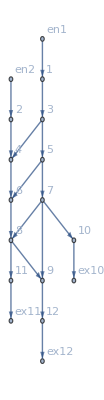

```mathematica
d2e["FG"]
```

```mathematica
Get[dddRicardo]
DataNoSplt=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{
{5,7,9,4001},{10,7,9,4001},{8,7,9,4001},
{11,8,9,4001},{6,8,9,4001},{7,8,9,4001}(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2eNoSplt=Data2Equations[DataNoSplt/.{I1->1000,I2->1000,U1->0,U2->0,U3->0}];
critNoSplt=CriticalCongestionSolver[d2eNoSplt];//AbsoluteTiming
```

Iterative DNF convertion...

... took 31.2945 seconds to terminate. 
Removing duplicates and reducing...

... took 0.018657 seconds to terminate.

Iterative DNF convertion...

... took 7.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

... took 0.000198 seconds to terminate.

Iterative DNF convertion...

... took 5.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

... took 0.000166 seconds to terminate.

Iterative DNF convertion...

... took 6.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

... took 0.000174 seconds to terminate.

MFGSS: Multiple solutions: -3001.≤u19≤0.

Picked one value for the variable(s) {u19} {-2974.} (respectively)

{32.4182,Null}

```mathematica
IsNonLinearSolution[critNoSplt][critNoSplt["AssoCritical"]]
```

All restrictions are True

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {-1.13687×10^-12,-1.13687×10^-12,0.,-1.13687×10^-12,-1.13687×10^-12,0.,-1.13687×10^-12,-1.13687×10^-12,0.,0.,-1.13687×10^-12,0.,-1.13687×10^-12,0.}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 1.13687×10^-12

<|u1→4000.,u2→3000.,u3→4000.,u4→3000.,u5→3000.,u6→3000.,u7→3000.,u8→2000.,u9→3000.,u10→2000.,u11→2000.,u12→2000.,u13→2000.,u14→1000.,u15→2000.,u16→1000.,u17→1000.,u18→1000.,u19→-2974.,u20→-2974.,u21→1000.,u22→0.,u23→-2974.,u24→-2974.,u25→1000.,u26→0.,u27→-2974.,u28→-2974.,u29→0.,u30→0.,u31→0.,u32→0.,u33→0.,u34→0.,u35→4000.,u36→4000.,u37→4000.,u38→4000.,j1→0.,j2→1000.,j3→0.,j4→1000.,j5→0.,j6→0.,j7→0.,j8→1000.,j9→0.,j10→1000.,j11→0.,j12→0.,j13→0.,j14→1000.,j15→0.,j16→1000.,j17→0.,j18→0.,j19→0.,j20→0.,j21→0.,j22→1000.,j23→0.,j24→0.,j25→0.,j26→1000.,j27→0.,j28→0.,j29→0.,j30→1000.,j31→0.,j32→1000.,j33→0.,j34→0.,j35→0.,j36→1000.,j37→0.,j38→1000.,jt1→0.,jt2→1000.,jt3→0.,jt4→1000.,jt5→0.,jt6→1000.,jt7→0.,jt8→0.,jt9→0.,jt10→0.,jt11→0.,jt12→1000.,jt13→0.,jt14→0.,jt15→0.,jt16→0.,jt17→0.,jt18→1000.,jt19→0.,jt20→0.,jt21→0.,jt22→0.,jt23→0.,jt24→1000.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→0.,jt31→1000.,jt32→0.,jt33→0.,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt39→0.,jt40→0.,jt41→0.,jt42→0.,jt43→1000.,jt44→0.,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt50→0.,jt51→0.,jt52→0.,jt53→0.,jt54→0.,jt55→0.,jt56→0.,jt57→0.,jt58→0.,jt59→1000.,jt60→0.,jt61→1000.,jt62→0.,jt63→0.,jt64→0.|>

Iterative DNF convertion...

Iterative DNF convertion took 30.846 seconds to terminate. 
Removing duplicates and reducing...

Iterative DNF convertion...

Iterative DNF convertion took 7.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

Iterative DNF convertion...

Iterative DNF convertion took 4.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

Iterative DNF convertion...

Iterative DNF convertion took 4.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

MFGSS: Multiple solutions: -3001.≤u19≤0.

Picked one value for the variable(s) {u19} {-2974.} (respectively)

{31.9327,Null}

Iterative DNF convertion took 31.9716 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -3001.≤u19≤0.

Picked one value for the variable(s) {u19} {-2974.} (respectively)

{33.0927,Null}

Iterative DNF convertion took 32.1124 seconds to terminate

Iterative DNF convertion took 0.106322 seconds to terminate

Iterative DNF convertion took 0.015021 seconds to terminate

Iterative DNF convertion took 0.010981 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -3001.≤u19≤0.

Picked one value for the variable(s) {u19} {-2974.} (respectively)

{33.4,Null}

Iterative DNF convertion took 32.4519 seconds to terminate

Iterative DNF convertion took 0.119409 seconds to terminate

Iterative DNF convertion took 0.016928 seconds to terminate

Iterative DNF convertion took 0.012381 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -3001.≤u19≤0.

Picked one value for the variable(s) {u19} {-2974.} (respectively)

{33.8057,Null}

Iterative DNF convertion took 32.7087 seconds to terminate

Iterative DNF convertion took 0.11252 seconds to terminate

Iterative DNF convertion took 0.015535 seconds to terminate

Iterative DNF convertion took 0.011943 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -3001.≤u19≤0.

Picked one value for the variable(s) {u19} {-2974.} (respectively)

{33.931,Null}

{34.2689,Null}

Iterative DNF convertion took 69.4619 seconds to terminate

Iterative DNF convertion took 0.47554 seconds to terminate

Iterative DNF convertion took 0.012635 seconds to terminate

Iterative DNF convertion took 0.016156 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -3001≤u19≤0

Picked one value for the variable(s) {u19} {-2974} (respectively)

{71.1561,Null}

Iterative DNF convertion took 68.8192 seconds to terminate

Iterative DNF convertion took 0.56005 seconds to terminate

Iterative DNF convertion took 0.015319 seconds to terminate

Iterative DNF convertion took 0.014922 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -3001≤u19≤0

Picked one value for the variable(s) {u19} {-2974} (respectively)

{70.7355,Null}

```mathematica
Get[dddRicardo]
DataNoSplt=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{
{5,7,9,4001},{10,7,9,4001},{8,7,9,4001},
{11,8,9,4001},{6,8,9,4001},{7,8,9,4001}(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2eNoSplt=Data2Equations[DataNoSplt/.{I1->1000,I2->1000,U1->0,U2->0,U3->0}];
{B,K,cost,vars}=GetKirchhoffMatrix[d2eNoSplt];
```

```mathematica
Get[dddRicardo]
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e=Data2Equations[Data/.{I1->1000,I2->1000,U1->0,U2->0,U3->0}];
critSplt=CriticalCongestionSolver[d2e];//AbsoluteTiming
```

0: (jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(jt10==0||jt17+jt18==0)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(jt27+jt28==0||4 (jt17+jt18)==5000+4 jt10+jt27+jt28)&&(jt32+jt33+jt34==0||11 (jt17+jt18)==11000+11 jt10+jt32+jt33+jt34)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(jt10==0||jt11+jt16==0)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt17==0||jt19==0)&&(jt18==0||jt10==jt19)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt29==0||jt32==0)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt45==0||jt48==0)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||5000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(38000+38 jt10+jt22+jt34+jt37==37 jt17+37 jt18+jt19+jt29+jt30||47000+44 jt10+jt22+jt34+jt37==43 jt17+43 jt18+jt19+jt29+jt30+u1)&&(35 jt10+2 (16500+jt22+jt34+jt37)==33 jt17+33 jt18+2 (jt19+jt29+jt30)||46000+52 jt10+3 jt22+3 jt34+3 jt37+u1==49 jt17+49 jt18+3 (jt19+jt29+jt30))

1: (35 jt10+2 (16500+jt22+jt34+jt37)==33 jt17+33 jt18+2 (jt19+jt29+jt30)||46000+52 jt10+3 jt22+3 jt34+3 jt37+u1==49 jt17+49 jt18+3 (jt19+jt29+jt30))&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(38000+38 jt10+jt22+jt34+jt37==37 jt17+37 jt18+jt19+jt29+jt30||47000+44 jt10+jt22+jt34+jt37==43 jt17+43 jt18+jt19+jt29+jt30+u1)&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||5000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt32+jt33+jt34==0||11 (jt17+jt18)==11000+11 jt10+jt32+jt33+jt34)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(jt27+jt28==0||4 (jt17+jt18)==5000+4 jt10+jt27+jt28)&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt10==0||jt17+jt18==0)&&(jt10==0||jt11+jt16==0)&&(jt45==0||jt48==0)&&(jt42==0||jt47==0)&&(jt41==0||jt44==0)&&(jt29==0||jt32==0)&&(jt18==0||jt10==jt19)&&(jt17==0||jt19==0)

Iterative DNF convertion took 4.65421 seconds to terminate.

Reducing took 0.007627 seconds to terminate.

{5.59623,Null}

Iterative DNF convertion took 4.84015 seconds to terminate

Iterative DNF convertion took 0.097742 seconds to terminate

Iterative DNF convertion took 0.007525 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{5.81485,Null}

Iterative DNF convertion took 5.27945 seconds to terminate

Iterative DNF convertion took 0.074018 seconds to terminate

Iterative DNF convertion took 0.003639 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{5.96865,Null}

Iterative DNF convertion took 34.4623 seconds to terminate

Iterative DNF convertion took 0.188789 seconds to terminate

Iterative DNF convertion took 0.003909 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

{35.4993,Null}

Iterative DNF convertion took 23.213 seconds to terminate

Iterative DNF convertion took 0.185029 seconds to terminate

Iterative DNF convertion took 0.005296 seconds to terminate

Iterative DNF convertion took 4.×10^-6 seconds to terminate

{24.3659,Null}

```mathematica
IsNonLinearSolution[critSplt][critSplt["AssoCritical"]]
```

All restrictions are True

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {-1.13687×10^-12,-1.13687×10^-12,0.,-1.13687×10^-12,-1.13687×10^-12,0.,-1.13687×10^-12,-1.13687×10^-12,0.,-2.84217×10^-13,-7.95808×10^-13,-2.84217×10^-13,-7.95808×10^-13,-5.68434×10^-13}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 1.13687×10^-12

<|u1→3750.,u2→2750.,u3→3750.,u4→2750.,u5→2750.,u6→2750.,u7→2750.,u8→1750.,u9→2750.,u10→1750.,u11→1750.,u12→1750.,u13→1750.,u14→750.,u15→1750.,u16→750.,u17→750.,u18→750.,u19→750.,u20→500.,u21→750.,u22→0.,u23→750.,u24→500.,u25→750.,u26→0.,u27→500.,u28→0.,u29→0.,u30→0.,u31→0.,u32→0.,u33→0.,u34→0.,u35→3750.,u36→3750.,u37→3750.,u38→3750.,j1→0.,j2→1000.,j3→0.,j4→1000.,j5→0.,j6→0.,j7→0.,j8→1000.,j9→0.,j10→1000.,j11→0.,j12→0.,j13→0.,j14→1000.,j15→0.,j16→1000.,j17→0.,j18→0.,j19→0.,j20→250.,j21→0.,j22→750.,j23→0.,j24→250.,j25→0.,j26→750.,j27→0.,j28→500.,j29→0.,j30→750.,j31→0.,j32→750.,j33→0.,j34→500.,j35→0.,j36→1000.,j37→0.,j38→1000.,jt1→0.,jt2→1000.,jt3→0.,jt4→1000.,jt5→0.,jt6→1000.,jt7→0.,jt8→0.,jt9→0.,jt10→0.,jt11→0.,jt12→1000.,jt13→0.,jt14→0.,jt15→0.,jt16→0.,jt17→0.,jt18→1000.,jt19→0.,jt20→0.,jt21→0.,jt22→0.,jt23→0.,jt24→1000.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→250.,jt31→750.,jt32→0.,jt33→0.,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt39→0.,jt40→0.,jt41→0.,jt42→250.,jt43→750.,jt44→0.,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt50→0.,jt51→0.,jt52→0.,jt53→0.,jt54→250.,jt55→0.,jt56→250.,jt57→0.,jt58→0.,jt59→750.,jt60→0.,jt61→750.,jt62→0.,jt63→500.,jt64→0.|>

```mathematica
Get[dddRicardo]
(*this has large but not infinity costs on entrance and exits*)
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e=Data2Equations[Data/.{I1->1000,I2->1000,U1->0,U2->0,U3->0}];
critSplt=CriticalCongestionSolver[d2e];//AbsoluteTiming
```

0: {True,jt10≥0&&jt11≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥3000+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&11000+11 jt10+jt32+jt33+jt34≥11 jt17+11 jt18+jt29&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45≥22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33&&5000+8 jt10+jt19+jt29+jt30+u1≤9 jt17+9 jt18+jt22+jt34+jt37&&43 jt17+43 jt18+jt19+jt29+jt30+u1≤47000+44 jt10+jt22+jt34+jt37&&46000+52 jt10+3 jt22+3 jt34+3 jt37+u1≤49 jt17+49 jt18+3 jt19+3 jt29+3 jt30&&jt11≤1000&&jt19+jt32≤jt10+jt22&&4 jt17+4 jt18+jt41+jt42≤5000+4 jt10+jt27+jt28&&jt11+jt16≤jt17+jt18&&jt17+jt18≤1000+jt11+jt16&&jt27≤jt16&&jt16≤jt17+jt22+jt27&&3000+3 jt10+jt19≤4 jt17+3 jt18+jt22&&3000+3 jt10+jt28≤4 jt17+3 jt18+jt22&&5 jt17+4 jt18+jt22≤5000+4 jt10+jt16+jt28&&jt17+jt18≤2000+jt10+jt16&&11 jt17+11 jt18+jt44+jt45≤11000+11 jt10+jt32+jt33+jt34&&jt44+jt47≤jt27+jt28&&jt41+jt48≤jt32+jt33+jt34&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&33000+35 jt10+2 jt22+2 jt34+2 jt37≤33 jt17+33 jt18+2 jt19+2 jt29+2 jt30&&11000+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37≤11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48&&22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48≤22 jt17+22 jt18+jt19+jt27+jt28+jt29+2 jt30+jt32+2 jt33,(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(jt10==0||jt17+jt18==0)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(4 jt17+3 jt18+jt22==3000+3 jt10||jt17+jt22==0)&&(jt10+jt22==jt19||4 jt17+4 jt18+jt22==3000+3 jt10+jt19)&&(jt27+jt28==0||4 (jt17+jt18)==5000+4 jt10+jt27+jt28)&&(jt32+jt33+jt34==0||11 jt17+11 jt18==11000+11 jt10+jt32+jt33+jt34)&&(11 jt17+11 jt18+jt19+jt29==11000+12 jt10+jt22+jt33+jt34+jt37||jt30+jt33==0)&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(jt10==0||jt11+jt16==0)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt17==0||jt19==0)&&(jt18==0||jt10==jt19)&&(4 jt17+3 jt18+jt22==3000+3 jt10+jt19||jt22==0)&&(4 jt17+3 jt18+jt22==3000+3 jt10+jt28||jt16==jt27)&&(5 jt17+4 jt18+jt22==5000+4 jt10+jt16+jt28||jt27==0)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt29==0||jt32==0)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt33==0||11 jt17+11 jt18+jt29==11000+11 jt10+jt32+jt33+jt34)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(4 jt17+4 jt18+jt41+jt42==5000+4 jt10+jt27+jt28||jt27+jt28==jt44+jt47)&&(jt45==0||jt48==0)&&(11 jt17+11 jt18+jt44+jt45==11000+11 jt10+jt32+jt33+jt34||jt32+jt33+jt34==jt41+jt48)&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||11 jt17+11 jt18+jt19+jt29==11000+12 jt10+jt22+jt33+jt34+jt37)&&(4 jt17+4 jt18+jt22+jt34+jt37==3000+3 jt10+jt19+jt29+jt30||5000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(38000+38 jt10+jt22+jt34+jt37==37 jt17+37 jt18+jt19+jt29+jt30||43 jt17+43 jt18+jt19+jt29+jt30+u1==47000+44 jt10+jt22+jt34+jt37)&&(33000+35 jt10+2 jt22+2 jt34+2 jt37==33 jt17+33 jt18+2 jt19+2 jt29+2 jt30||46000+52 jt10+3 jt22+3 jt34+3 jt37+u1==49 jt17+49 jt18+3 jt19+3 jt29+3 jt30)}

1: {True,jt10≥0&&jt11≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥3000+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&11000+11 jt10+jt32+jt33+jt34≥11 jt17+11 jt18+jt29&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45≥22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33&&5000+8 jt10+jt19+jt29+jt30+u1≤9 jt17+9 jt18+jt22+jt34+jt37&&43 jt17+43 jt18+jt19+jt29+jt30+u1≤47000+44 jt10+jt22+jt34+jt37&&46000+52 jt10+3 jt22+3 jt34+3 jt37+u1≤49 jt17+49 jt18+3 (jt19+jt29+jt30)&&jt11≤1000&&jt19+jt32≤jt10+jt22&&4 jt17+4 jt18+jt41+jt42≤5000+4 jt10+jt27+jt28&&jt11+jt16≤jt17+jt18&&jt17+jt18≤1000+jt11+jt16&&jt27≤jt16&&jt16≤jt17+jt22+jt27&&3000+3 jt10+jt19≤4 jt17+3 jt18+jt22&&3000+3 jt10+jt28≤4 jt17+3 jt18+jt22&&5 jt17+4 jt18+jt22≤5000+4 jt10+jt16+jt28&&jt17+jt18≤2000+jt10+jt16&&11 jt17+11 jt18+jt44+jt45≤11000+11 jt10+jt32+jt33+jt34&&jt44+jt47≤jt27+jt28&&jt41+jt48≤jt32+jt33+jt34&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&35 jt10+2 (16500+jt22+jt34+jt37)≤33 jt17+33 jt18+2 (jt19+jt29+jt30)&&11000+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37≤11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48&&22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48≤22 jt17+22 jt18+jt19+jt27+jt28+jt29+2 jt30+jt32+2 jt33,(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(jt10==0||jt17+jt18==0)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(jt27+jt28==0||4 (jt17+jt18)==5000+4 jt10+jt27+jt28)&&(jt32+jt33+jt34==0||11 (jt17+jt18)==11000+11 jt10+jt32+jt33+jt34)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(jt10==0||jt11+jt16==0)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt17==0||jt19==0)&&(jt18==0||jt10==jt19)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt29==0||jt32==0)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt45==0||jt48==0)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||5000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(38000+38 jt10+jt22+jt34+jt37==37 jt17+37 jt18+jt19+jt29+jt30||47000+44 jt10+jt22+jt34+jt37==43 jt17+43 jt18+jt19+jt29+jt30+u1)&&(35 jt10+2 (16500+jt22+jt34+jt37)==33 jt17+33 jt18+2 (jt19+jt29+jt30)||46000+52 jt10+3 jt22+3 jt34+3 jt37+u1==49 jt17+49 jt18+3 (jt19+jt29+jt30))}

Iterative DNF convertion took 5.13066 seconds to terminate.

Reducing took 0.009087 seconds to terminate.

0: {u1==3750&&jt48==0&&jt47==0&&jt45==0&&jt44==0&&jt42==250&&jt41==0&&jt37==0&&jt34==0&&jt33==0&&jt32==0&&jt30==250&&jt29==0&&jt28==0&&jt27==0&&jt22==0&&jt19==0&&jt18==1000&&jt17==0&&jt16==0&&jt11==0&&jt10==0,True,True}

1: {True,True,True}

{True,True,True}

{6.09857,Null}

Iterative DNF convertion...

... took 4.62555 seconds to terminate. 
Removing duplicates and reducing...

... took 0.005882 seconds to terminate.

Iterative DNF convertion...

... took 5.×10^-6 seconds to terminate. 
Removing duplicates and reducing...

... took 0.000059 seconds to terminate.

{5.46973,Null}

{5.48268,Null}

Iterative DNF convertion took 4.76683 seconds to terminate

Iterative DNF convertion took 0.096058 seconds to terminate

Iterative DNF convertion took 0.007089 seconds to terminate

Iterative DNF convertion took 3.×10^-6 seconds to terminate

{5.79336,Null}

```mathematica
??ZAnd
```

Iterative DNF convertion took 5.45181 seconds to terminate

Iterative DNF convertion took 0.16761 seconds to terminate

Iterative DNF convertion took 0.008081 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

{6.22325,Null}